```mathematica
ME=0.511;
MP=0.511;
MTotal=ME+MP;
k=16.7;
p=18.15;
randoms=RandomReal[{1,p-1},10000000];
energies=Table[{randoms[[i]],p-randoms[[i]],(randoms[[i]]-(p-randoms[[i]]))/p},{i,10000000}];
```

```mathematica
j=399998;
NSolve[k^2==2*energies[[j,1]]*energies[[j,2]]-2*√((energies[[j,1]])^2-(ME)^2)*√((energies[[j,2]])^2-(ME)^2)*cos+2*(ME)^2,cos]
```

{{cos→-3.05068}}

```mathematica
cosines=Table[(k^2-2*energies[[i,1]]*energies[[i,2]]-2*(ME)^2)/(-2*√((energies[[i,1]])^2-(ME)^2)*√((energies[[i,2]])^2-(ME)^2)),{i,10000000}];
```

```mathematica
finalData=Table[If[cosines[[k]]<= 1 && cosines[[k]]>=-1,{energies[[k,1]],energies[[k,2]],energies[[k,3]],cosines[[k]]},##&[]],{k,1,10000000}];
```

```mathematica
cosines=Select[cosines, # > -1 &];
cosines=Select[cosines,# < 1 &];
angles=Map[ArcCos,cosines];
```

```mathematica
newangles=(180/Pi)*angles;
```

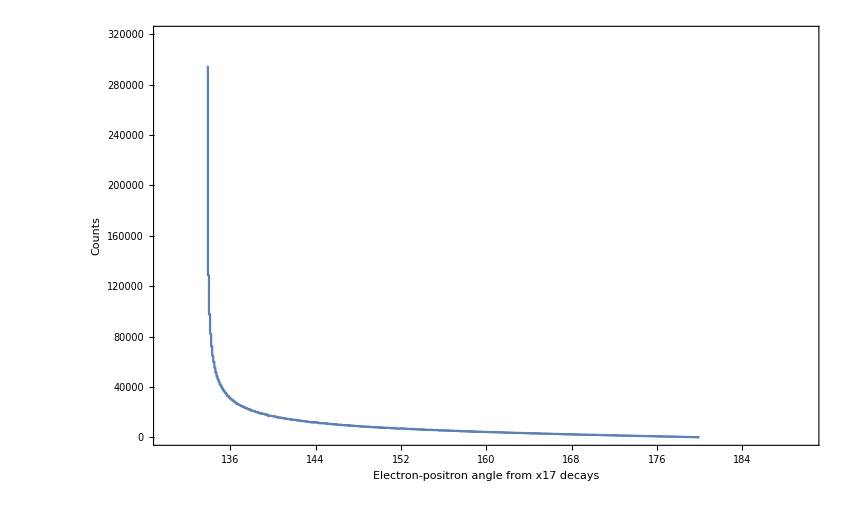

4392655

143.21

10.0528

```mathematica
hist=HistogramList[newangles,{.1}];

ListPlot[Transpose[{hist[[1]],ArrayPad[hist[[2]],{0,1},"Fixed"]}],InterpolationOrder->0,Joined->True,AxesOrigin->{0,0},PlotRange->{{130,190},{0,320000}},RotateLabel->True,FrameLabel->{Style["Electron-positron angle from x17 decays",20,Bold,Blue],Style["Counts",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
Length[newangles]
Mean[newangles]
StandardDeviation[newangles]
```

```mathematica
143.21738273604785
```

143.217

```mathematica
SetDirectory[NotebookDirectory[]];
Export["x17angles.txt",Flatten[finalData]]
```

$Aborted